```mathematica
pin[n_]=90/π^4 1/n^4;
fn[x_,n_]=1/6 n^4 x^3 Exp[-n x];

plank[x_]=15/π^4 x^3/(Exp[x]-1);
erlang[x_,n_]=(n^4 x^3 Exp[-n x])/(3!);
fnSample[n_]:=-1/n Log[RandomReal[]RandomReal[]RandomReal[]RandomReal[]];
```

```mathematica
Sum[pin[n]//N,{n,1,50}]
```

0.999998

```mathematica
NN=100000;
sample=Table[0,{i,1,NN}];
For[j=1,j<=NN,j++,
pintotal=0;
test=RandomReal[];
For[i=1,i<=50,i++,
pintotal = pintotal+pin[i];
If[test<pintotal,
sample[[j]]=fnSample[i];
Break[];
];
];
];
```

```mathematica
Length[sample]
```

100000

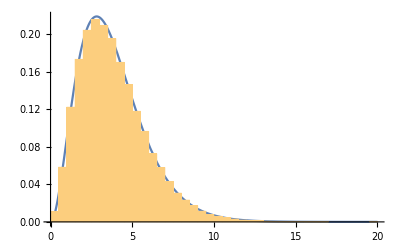

```mathematica
pa=Plot[{plank[x]},{x,0,20}];
pb=Histogram[sample,50,"PDF"];
Show[pa,pb]
```

```mathematica
hbar=1.0546 10^-27;
T=3;
kb=1.38064852  10^-16;
vd=6;
(*Clear[hbar,T,kb,vd]*)

plankR[ω_]=15((kb π T)/hbar)^-4 ω^3/(Exp[(hbar ω)/(kb T)]-1);
fnR[ω_,n_]=1/6 n^4(hbar/(kb T))^4 ω^3 Exp[-n (hbar ω)/(kb T)];
pinR[n_]=90/π^4 1/n^4;
fnSampleR[n_]:=-(1/(hbar/(kb T)n))Log[RandomReal[]RandomReal[]RandomReal[]RandomReal[]];
```

```mathematica
NN=100000;
sample=Table[0,{i,1,NN}];
For[j=1,j<=NN,j++,
pintotal=0;
For[i=1,i<=50,i++,
test=RandomReal[];
pintotal = pintotal+pinR[i];
If[test<pintotal,
sample[[j]]=fnSampleR[i];
Break[];
];
];
];
```

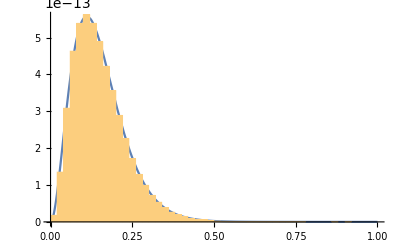

```mathematica
pa=Plot[{plankR[x]},{x,0,10^13}];
pb=Histogram[sample,50,"PDF"];
Show[pa,pb]
```

```mathematica
Integrate[ω plankR[ω],{ω,0,∞},Assumptions->Re[hbar/(kb T)]>0]
```

1.50511×10^12

```mathematica
Integrate[(3 hbar)/(2 π^2 vd^3)ω^3/(Exp[(hbar ω)/(kb T)]-1),{ω,0,∞},Assumptions->Re[hbar/(kb T)]>0]
```

(kb^4 π^2 T^4)/(10 hbar^3 vd^3)